# Rotating disk electrode voltammetry

## Fully implicit scheme

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameLabel-> {
Style["increment",FontFamily-> "Arial" ,FontSize->  12,FontColor->Black],
Style["χ",FontFamily->  "Times New Roman" ,FontSize->   12, FontWeight->   "Plain",FontColor-> Black],
None,
None}
};
```

```mathematica
optionB={
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["χ",FontFamily-> "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeRDEDiagonals];

makeRDEDiagonals[m_Integer,d_][zMax_]:=Module[{x,y,z},
x=Table[-d+(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3),{j,3,m-1}];
z=Table[-d-(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3),{j,2,m-2}];
y=Table[1.+2.*d,{j,2,m-1}];
{x,y,z}]
```

```mathematica
Clear[𝔻,zMax,x,y,z];
{x,y,z}=makeRDEDiagonals[7,𝔻][zMax]
```

{{-𝔻+0.0197681 zMax^3 𝔻,-𝔻+0.0444783 zMax^3 𝔻,-𝔻+0.0790726 zMax^3 𝔻,-𝔻+0.123551 zMax^3 𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻-0.00494204 zMax^3 𝔻,-𝔻-0.0197681 zMax^3 𝔻,-𝔻-0.0444783 zMax^3 𝔻,-𝔻-0.0790726 zMax^3 𝔻}}

```mathematica
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5] /. {zMax->2.,𝔻->1.*^1}//MatrixForm
```

(1.+2. 𝔻 | -𝔻-0.00494204 zMax^3 𝔻 | 0 | 0 | 0
-𝔻+0.0197681 zMax^3 𝔻 | 1.+2. 𝔻 | -𝔻-0.0197681 zMax^3 𝔻 | 0 | 0
0 | -𝔻+0.0444783 zMax^3 𝔻 | 1.+2. 𝔻 | -𝔻-0.0444783 zMax^3 𝔻 | 0
0 | 0 | -𝔻+0.0790726 zMax^3 𝔻 | 1.+2. 𝔻 | -𝔻-0.0790726 zMax^3 𝔻
0 | 0 | 0 | -𝔻+0.123551 zMax^3 𝔻 | 1.+2. 𝔻)

```mathematica
{x,y,z}=makeRDEDiagonals[7,10.][2.];
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5]//MatrixForm
```

(21. | -10.3954 | 0 | 0 | 0
-8.41855 | 21. | -11.5815 | 0 | 0
0 | -6.44173 | 21. | -13.5583 | 0
0 | 0 | -3.67419 | 21. | -16.3258
0 | 0 | 0 | -0.115926 | 21.)

```mathematica
makeDiagonals[7]
```

makeDiagonals[7]

```mathematica
(Table[Switch[j-i,-1,x⟦j+1⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]/. {zMax->2.,𝔻->1.*^1})//MatrixForm
```

(21. | -10.3954 | 0 | 0
-6.44173 | 21. | -11.5815 | 0
0 | -3.67419 | 21. | -13.5583
0 | 0 | -0.115926 | 21.)

## Set Up Solution

```mathematica
Clear[implicitSolveRDE];

implicitSolveRDE[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_,zMax_}]:=Module[{x,y,z,len,mat,x1,y1,z1,initial,range,τ,solveNext,zM},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeRDEDiagonals[m,d][zMax];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
x1=-d+(2.13496*zMax^3*d)/(2.*(m-1)^3);
y1=y⟦1⟧;
z1=z⟦1⟧;
zM=-d-(2.13496*zMax^3*d*(j-1)^2)/(2.*(m-1)^3)/.j-> (m-1);

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},
ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧-=(tmp*x1*ksStar*ξ^(1.-α));
b⟦-1⟧-=zM;
mat⟦1,1⟧=y1+4.*x1*tmp;
mat⟦1,2⟧=z1-x1*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]];

Rest@FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)

f=F/(R*T);
```

### Electrochemical variables

```mathematica
Clear[α,𝒟,upperLimit,lowerLimit,𝕥];

α=0.5 (*transfer coefficient*);

𝒟=1.*^-5;(*diffusion coefficient*)

lowerLimit=-10.(*limit = f×(E-E^o)*);

upperLimit=10.(*limit = f×(E-E^o)*);

𝕥=2*(upperLimit+Abs[lowerLimit]);
```

### Simulation variables

```mathematica
Clear[n,Δ,zMax,τ,𝔻,m,ksDim,ksStar];

n=400;

Δ=3.;

τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)

zMax=2.;

𝔻=1.*^1;
m=1+Ceiling[zMax*√((Δ*𝔻)/τ)];
ksDim=20.;

ksStar=2.*ksDim*zMax/(m-1);
```

```mathematica
{n,Δ,zMax,τ,𝔻,m,ksDim,ksStar}
```

{400,3.,2.,0.100251,10.,36,20.,2.28571}

## Solve

```mathematica
c=implicitSolveRDE[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α,zMax}];
```

## Plot RDE voltammogram

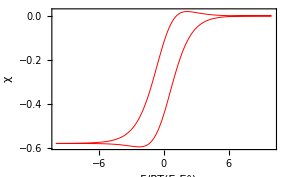

```mathematica
rde=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*1/Δ^(1/2)*(m-1)/(2.*zMax))&,c];

rde2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],rde⟦j⟧},{j,1,Length[rde]}];

plot2=ListPlot[rde2,optionB,PlotRange->All]
```